# Lección 5 - Programación en Wolfram y cadenas

## Escribiendo código limpio en Wolfram Language

Se favorece la programación funcional

Generación de listas

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Mismo resultado pero con un paradigma imperativo (no recomendado)

```mathematica
Module[{list,i}, list={}; For[i=1,i≤10,i++, list=Append[list,i^2]];list]
```

{1,4,9,16,25,36,49,64,81,100}

Construir número con elementos de una lista

```mathematica
fromdigits[{h_,t_,o_}]:=100h+10t+o
```

```mathematica
fromdigits[{5,6,1}]
```

561

Generalizando a una lista de n elementos

```mathematica
fromdigits[list_List]:=Total[Table[10^(Length[list]-i)*list[[i]],{i,Length[list]}]]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Genera las potencias de 10 de una forma más directa

```mathematica
fromdigits[list_List]:=Total[10^Reverse[Range[Length[list]]-1]*list]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Muestra ciertos pasos del proceso de  evaluación

```mathematica
Trace[fromdigits[{5,6,1,7,8}],Total]
```

{Total[10^Reverse[Range[Length[{5,6,1,7,8}]]-1] {5,6,1,7,8}],Total[{50000,6000,100,70,8}],56178}

Enfoque recursivo

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[{k_}]:=k
```

```mathematica
fromdigits[{digits___,k_}]:=10*fromdigits[{digits}]+k
```

```mathematica
fromdigits[{1,5,6,7}]
```

1567

Muestra le evaluación recursiva

```mathematica
Trace[fromdigits[{1,5,6,7}]]
```

{fromdigits[{1,5,6,7}],10 fromdigits[{1,5,6}]+7,{{fromdigits[{1,5,6}],10 fromdigits[{1,5}]+6,{{fromdigits[{1,5}],10 fromdigits[{1}]+5,{{fromdigits[{1}],1},10 1,10},10+5,15},10 15,150},150+6,156},10 156,1560},1560+7,1567}

Hasta que te das cuenta que el problema es ideal para un Fold!

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[list_]:=Fold[10*#1+#2&,list]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Por supuesto tambíen existe una función del sistema

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

Hay que buscar balance entre simpleza y entendimiento del código

```mathematica
ClearAll[fromdigits];
fromdigits =Fold[{10,1}.{##}&,#]& ;
```

```mathematica
fromdigits[{3,7,8,9}]
```

3789

Puede ser mejor separar tus definiciones en casos bien delimitados

```mathematica
fib[n_]:=If[!IntegerQ[n]||n<1,"Error",If[n==1||n==2,1,fib[n-1]+fib[n-2]]]
```

Esto se lee mejor

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n-1]+fib[n-2]
```

Nombrar bien a tus funciones. Qué nombre le darías a esto y cuales serían tus argumentos?

```mathematica
Graphics[{White,Riffle[NestList[Scale[Rotate[#,0.1],0.9]&,Rectangle[ ],40],{Pink,Yellow}]}]
```

-Graphics-

Cita del libro

“There’s a function DigitCount that counts the number of times different digits occur in an integer. Worse names for this function might be TotalDigits (confusing with IntegerLength), IntegerTotals (might be about adding up the integer somehow), PopulationCount (weird and whimsical), etc. “

Digitos de un número al revés

```mathematica
FromDigits[Reverse[IntegerDigits[123456]]]
```

654321

Existen muy funciones especificas que pueden simplificar el código

```mathematica
IntegerReverse[123456]
```

Uso de Timing

```mathematica
Timing[fib[25]]
```

{0.078125,75025}

Tiempo de ejecución crece de forma exponencial

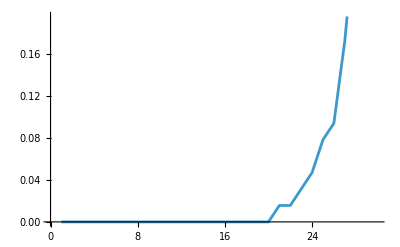

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,30}]]
```

Definición con memoización

```mathematica
ClearAll[fib]
```

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n]=fib[n-1]+fib[n-2]
```

Se puede computar hasta fib[1000] sin problema alguno

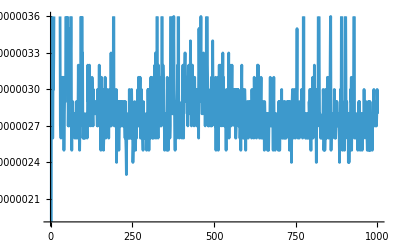

```mathematica
ListLinePlot[Table[First[AbsoluteTiming[fib[n]]],{n,1000}]]
```

Uso de opciones un plot

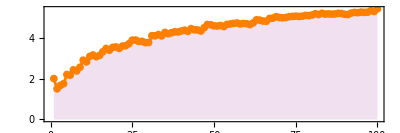

```mathematica
ListLinePlot[Table[Prime[n]/n,{n,100}],Frame->True, PlotStyle->Orange,Filling->Axis, 
FillingStyle->LightPurple,AspectRatio->1/3,Mesh->All]
```

Iconizar opciones

```mathematica
ListLinePlot[Table[Prime[n]/n,{n,100}],]
```

-Graphics-

Usar Iconize

```mathematica
Iconize[Table[Prime[n],{n,1000}]]
```

## Detecta errores en tu código

Texto rojo automático

```mathematica
WordCloud[Nest[Join[#,Length[ ]+Reverse[#,1,2]]&,{0},m],Spacings->0]
```

Mensajes de error

```mathematica
First[Cases[{1,2,3,4},777]]
```

First::nofirst: {} has zero length and no first element.

First[{}]

En ciertos casos simplemente no se evalúa

```mathematica
Graph[{a,b,c}]
```

Graph[{a,b,c}]

Gráficos con valores simbolicos no pueden ser mostrados

```mathematica
Graphics[{Circle[{0,0}],Disk[{a,b}]}]
```

-Graphics-

Probar una función con un valor

```mathematica
With[{m=4},Nest[Join[#,Length[#]+Reverse[#]]&,{0},m]]
```

{0,1,3,2,6,7,5,4,12,13,15,14,10,11,9,8}

Visualiza que hace el código

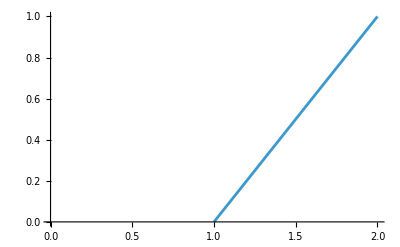
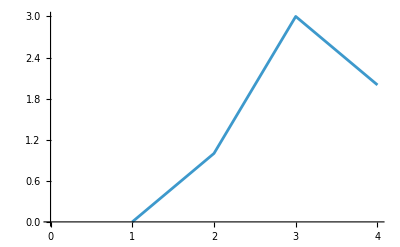
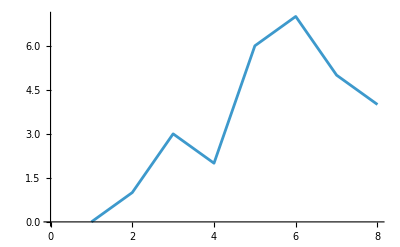
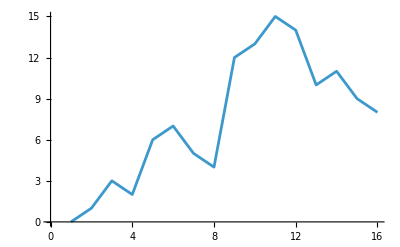
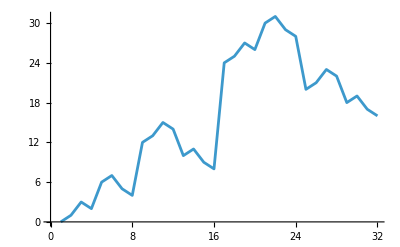
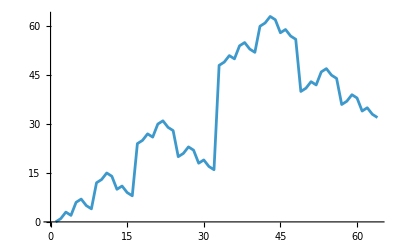

```mathematica
ListLinePlot/@Table[Nest[Join[#,Length[#]+Reverse[#]]&,{0},m],{m,6}]
```

Si está correcto debe tener los números de 0 a 2^m-1

```mathematica
Sort[With[{m=4},Nest[Join[#,Length[#]+Reverse[#]]&,{0},m]]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

Verifica la igualdad para diferentes m

```mathematica
Table[Sort[Nest[Join[#,Length[#]+Reverse[#]]&,{0},m]]==Range[0,2^m-1],{m,10}]
```

{True,True,True,True,True,True,True,True,True,True}

Impresión de valores sin interferir con la evaluación

```mathematica
Table[Echo[n]^2,{n,3}]
```

1

2

3

{1,4,9}

Monitorea el progreso

```mathematica
Monitor[Table[PrimeQ[2^(2^n)+1],{n,15}],Framed[n]]
```

{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False}

Reap captura el resultado final, y Sow permite devolver resultados intermedios

```mathematica
Reap[Total[Table[Sow[n],{n,5}]]]
```

{15,{{1,2,3,4,5}}}

```mathematica
Last@Reap[Nest[Join[#,Sow[Length[#]]+Reverse[#]]&,{0},10]]
```

{{1,2,4,8,16,32,64,128,256,512}}

## Patrones de cadenas

Busca el + junto a cualquier caracter

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_]
```

{+s,+p,+q,+e}

Tres caracteres adicionales

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_~~_~~_]
```

{+str,+pat,+qui,+eas}

Similar to Cases puede incluir una transformación

```mathematica
StringCases["+string +patterns are +quite +easy", ("+"~~x_)->Framed[x]]
```

{s,p,q,e}

Los Blank funcionan de la misma manera que hemos visto en otros patrones

```mathematica
StringCases["the [important] word", "["~~x__~~"]"->Framed[x]]
```

{important}

Tipicamente encuentra la secuencia más larga

```mathematica
StringCases["now [several] important [words]", "["~~x__~~"]"->Framed[x]]
```

{several] important [words}

Busca las más cortas

```mathematica
StringCases["now [several] important [words]", "["~~Shortest[x__]~~"]"->Framed[x]]
```

{several,words}

Reemplazo en cadenas

```mathematica
StringReplace["now [several] important [words]", {"["->"<<","]"->">>"}]
```

now <<several>> important <<words>>

Reemplazo y transformación

```mathematica
StringReplace["now [several] important [words]", "["~~Shortest[x__]~~"]":>ToUpperCase[x]]
```

now SEVERAL important WORDS

Aplica un reemplazo varias veces

```mathematica
NestList[StringReplace[#,{"A"->"AB","B"->"BA"}]&,"A",5]
```

{A,AB,ABBA,ABBABAAB,ABBABAABBAABABBA,ABBABAABBAABABBABAABABBAABBABAAB}

Cumplimiento del patron como función pura

```mathematica
Select[WordList[ ],StringMatchQ[#,"a"~~___~~"b"]&]
```

{absorb,adsorb,adverb,alb,aplomb}

A o B repetido

```mathematica
StringCases["the AAA and the BBB and the ABABBBABABABA",("A"|"B")..]
```

{AAA,BBB,ABABBBABABABA}

Secuencias de cadenas que representan .08números

```mathematica
StringCases["12 and 123 and 4567 and 0x456",DigitCharacter..]
```

{12,123,4567,0,456}

Incluir espacios en blanco

```mathematica
StringCases["12 and 123 and 4567 and 0x456",Whitespace~~DigitCharacter..~~Whitespace]
```

{ 123 , 4567 }

Genera una lista separando una cadena

```mathematica
StringSplit["a string to split"]
```

{a,string,to,split}

Especifica el delimitador

```mathematica
StringSplit["you+can+split--at+any--delimiter","+"|"--"]
```

{you,can,split,at,any,delimiter}

Delimitador caracter especial

```mathematica
StringSplit["first line
second line
third line","\n"]
```

{first line,second line,third line}

Insertar caracteres o cadenas en medio

```mathematica
StringRiffle[{"a","list","of","strings"},"---"]
```

a---list---of---strings

Unir cadenas

```mathematica
StringJoin["two to the ",TextString[50]," is ",TextString[2^50]]
```

two to the 50 is 1125899906842624

Strings con formas especificas que aceptan argumentos

```mathematica
StringTemplate["first `` then ``"][100,200]
```

first 100 then 200

Forzar la evaluación en el template

```mathematica
StringTemplate["2 to the 50 is <* 2^50 *>"][]
```

2 to the 50 is 1125899906842624

Referencia a un argumento en particular

```mathematica
StringTemplate["`1` to the `2` is <* #1^#2 *>"][2,50]
```

2 to the 50 is 1125899906842624

Otro ejemplo de evaluación

```mathematica
StringTemplate["the time now is <* Now *>"][ ]
```

the time now is Wed 11 Feb 2026 13:50:57